# 单轴拉伸

能量函数

```mathematica
tF = {{F11,F12,F13},{F21,F22,F23},{F31,F32,F33}};
tC = Transpose[tF].tF;
tI = IdentityMatrix[3];
tE = (tC-tI)/2;
```

```mathematica
c;Subscript[b, f];Subscript[b, t];Subscript[b, fs];
Q = Subscript[b, f] tE[[1,1]]^2 + Subscript[b, t](tE[[2,2]]^2+tE[[3,3]]^2+tE[[2,3]]^2+tE[[3,2]]^2)+ Subscript[b, fs](tE[[1,2]]^2+tE[[2,1]]^2+tE[[1,3]]^2+tE[[3,1]]^2);
W = (c/2)(Exp[Q]-1);
```

计算 ∂_F W

```mathematica
dWdF = D[W,{tF}];
```

初始化参数

```mathematica
F12 = 0.;
F13 =0.;
F21 =0.;
F23 =0.;
F31 =0.;
F32 =0.;
{c,Subscript[b, f],Subscript[b, t],Subscript[b, fs]} = {0.876,18.48,3.58, 1.627};
```

计算应力张量

```mathematica
ρ;
P = dWdF - ρ Transpose[Inverse[tF]];
sigma =1.0/Det[tF]* P Transpose[tF]; (*Det[tF]P Transpose[tF];*)
```

拉伸(应力)条件

## x轴

```mathematica
F22 = 1/Sqrt[F11];
F33 = 1/Sqrt[F11];
```

```mathematica
rho = Solve[{P[[2,2]]==0, P[[3,3]]==0}, {F11, ρ}][[1,1,2]];
(*定义拉伸范围*)
F11s = Table[i,{i,1,1.28,0.001}];
n = Dimensions[F11s];
rhos = Table[rho/.F11->lam,{lam,F11s}];
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

绘图

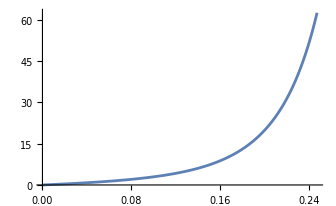

```mathematica
sigmas = Table[sigma/.{F11->F11s[[i]], ρ->rhos[[i]]},{i,n[[1]]}];
loglam = Log[F11s];
sig11 = Table[sigmas[[i,1,1]],{i,n[[1]]}];
myplot = Table[{loglam[[i]],sig11[[i]]},{i,n[[1]]}];
ListLinePlot[myplot]
```

## y轴

```mathematica
Clear[F11, F22,F33];
F11=1/(F22*F33);
solution = Solve[{P[[1,1]]==0, P[[3,3]]==0, F33>0}, {F33,ρ}, Reals];
solution/.F22->1.2
F22s = Table[i,{i,1,1.28,0.001}];
n = Dimensions[F22s];
f33srhos = Table[solution/.F22->lam, {lam, F22s}];
```

Solve::inex: Solve 无法求解具有不精确系数的系统或通过将系统中出现的不精确数直接合理化处理得到的系统. 由于 Solve 所用的许多方法需要精确输入，为 Solve 提供一个精确版本的系统可能会有帮助.

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

{{F33→0.850681,ρ→-0.402291}}

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

General::stop: 在本次计算中，Solve::ratnz 的进一步输出将被抑制.

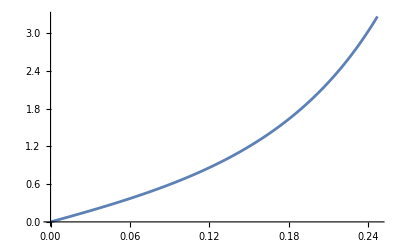

```mathematica
sigma/.{F22-> F22s[[200]],F33->f33srhos[[200,1,1,2]],ρ->f33srhos[[200,1,2,2]]};
sigmas = Table[sigma/.{F22-> F22s[[i]],F33->f33srhos[[i,1,1,2]],ρ->f33srhos[[i,1,2,2]]}, {i,n[[1]]}];
loglam2 = Log[F22s];
sig22 = Table[sigmas[[i,2,2]],{i,n[[1]]}];
myplot2 = Table[{loglam2[[i]],sig22[[i]]},{i,n[[1]]}];
ListLinePlot[myplot2]
```

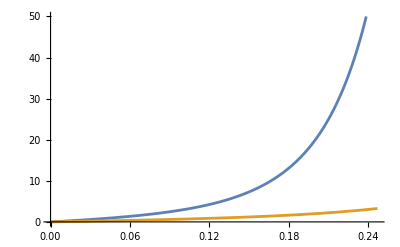

```mathematica
ListLinePlot[{myplot, myplot2},PlotRange->{0,50}]
```

```mathematica
1/(F22s[[150]] * f33srhos[[150,1,1,2]])
F22s[[150]]
f33srhos[[150,1,1,2]]
```